```mathematica
folder=NotebookDirectory[]
```

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/CNN_Exomoons/KOI-622.01/isochrones/

```mathematica
locations={"c1/dartmouth_starmodel_single.h5","c2/dartmouth_starmodel_single.h5","c3/dartmouth_starmodel_single.h5","c4/dartmouth_starmodel_single.h5","c5/dartmouth_starmodel_single.h5","c6/dartmouth_starmodel_single.h5","c7/dartmouth_starmodel_single.h5","c8/dartmouth_starmodel_single.h5","c9/dartmouth_starmodel_single.h5","c10/dartmouth_starmodel_single.h5","c11/dartmouth_starmodel_single.h5","c12/dartmouth_starmodel_single.h5"};
```

```mathematica
headers=Import[StringJoin[folder,locations[[1]]],{"Datasets","/samples/block0_items"}]
```

{age_0_0,mass_0_0,radius_0_0,logL_0_0,logg_0_0,Teff_0_0,Kepler_mag_0_0,age_0,feh_0,distance_0,AV_0,Kepler_mag,lnprob}

```mathematica
bestheaders={"Teff_0_0","logg_0_0","feh_0","mass_0_0","radius_0_0","age_0_0","logL_0_0","distance_0","AV_0"};
ints=Table[First[First[Position[headers,bestheaders[[i]]]]],{i,1,Length[bestheaders]}];
```

```mathematica
j=0;Label[jloop];j=j+1;Subscript[data, j]=Import[StringJoin[folder,locations[[j]]],{"Datasets","/samples/block0_values"}];If[j<Length[locations],Goto[jloop]];
```

```mathematica
combine=Flatten[Table[Subscript[data, jj],{jj,1,Length[locations]}],1];
Dimensions[combine]
combine=combine[[All,ints]];
Dimensions[combine]
```

{180300,13}

{180300,9}

```mathematica
starini=Import[StringJoin[folder,"star.ini"],"Table"];
select=Select[starini,#[[1]]=="parallax"&];
If[Length[select]==0,parallaxfound=0,parallaxfound=1];
If[parallaxfound==1,p=ToExpression[StringSplit[ToString[Flatten[select]],","][[3]]]];
If[parallaxfound==1,Δp=ToExpression[StringDelete[StringDelete[StringSplit[ToString[Flatten[select]],","][[5]],"}"]," "]]];
If[parallaxfound==1,maxdist=1000/Max[p-5Δp,10^-6],maxdist=∞];
If[parallaxfound==1,mindist=1000/(p+5Δp),mindist=0];
Dimensions[combine]
combine=Select[combine,mindist<#[[8]]<maxdist&];
Dimensions[combine]
```

{180300,9}

{179884,9}

```mathematica
rhoSun=(1.98855*10^30)/((4/3)π (6.955*10^8)^3);
rho=Table[rhoSun Extract[Extract[combine,i],4]/Extract[Extract[combine,i],5]^3,{i,1,Length[combine]}];
Print["test = ",Median[rho],"_{-",Median[rho]-Quantile[rho,0.5-0.5Erf[1/√2]],"}^{+",Quantile[rho,0.5+0.5Erf[1/√2]]-Median[rho],"}"]
```

test = 63.0243_{-19.4042}^{+26.483}

```mathematica
logtest=AndersonDarlingTest[RandomSample[Log10[rho],1000]]
lintest=AndersonDarlingTest[RandomSample[rho,1000]]
quastest=AndersonDarlingTest[RandomSample[rho^(2/3),1000]]
```

8.78633×10^-11

0.

0.

```mathematica
hereyago={{logtest,1},{lintest,2},{quastest,3}};
numero=Last[Last[Sort[hereyago]]];
If[Length[DeleteDuplicates[hereyago[[All,1]]]]==1,numero=1];If[numero==1,samp=Log[rho],If[numero==2,samp=rho,samp=rho^(2/3)]];
```

```mathematica
dummy={Median[samp],1.4286MedianDeviation[samp]};
```

```mathematica
If[numero==1,Print["log ρ = ",dummy]];
If[numero==2,Print["ρ = ",dummy]];
If[numero==3,Print["ρ^(2/3) = ",dummy]];
```

log ρ = {4.14352,0.345943}

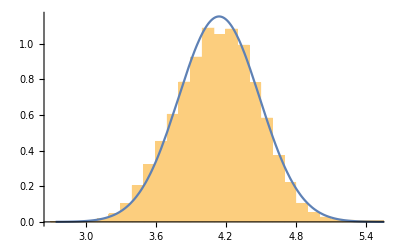

```mathematica
Show[Histogram[samp,Automatic,"PDF"],Plot[PDF[NormalDistribution[dummy[[1]],dummy[[2]]],x],{x,Min[samp],Max[samp]}]]
```

```mathematica
Export[StringJoin[folder,"post.dat"],combine,"Table"]
```

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/CNN_Exomoons/KOI-622.01/isochrones/post.dat